```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
<<TMtoCWTM`
```

```mathematica
<<ColoredToBinCWTM`
```

```mathematica
<<CWTMToTag`
```

```mathematica
<<TagToCT`
```

```mathematica
cWTMStep[rule:{(Rule|RuleDelayed)[{_,_},_]...},{head_,{s_,ss___}}]:={First[#],{ss,Splice[Last[#]]}}&[Replace[{head,s},rule]]
```

```mathematica
cWTM[rule:{(Rule|RuleDelayed)[{_,_},_]...},init:{_,_List},t_Integer:1]:=NestList[cWTMStep[rule,#]&,init,t]
```

```mathematica
tM=TuringMachine[{596440,2,3}];
```

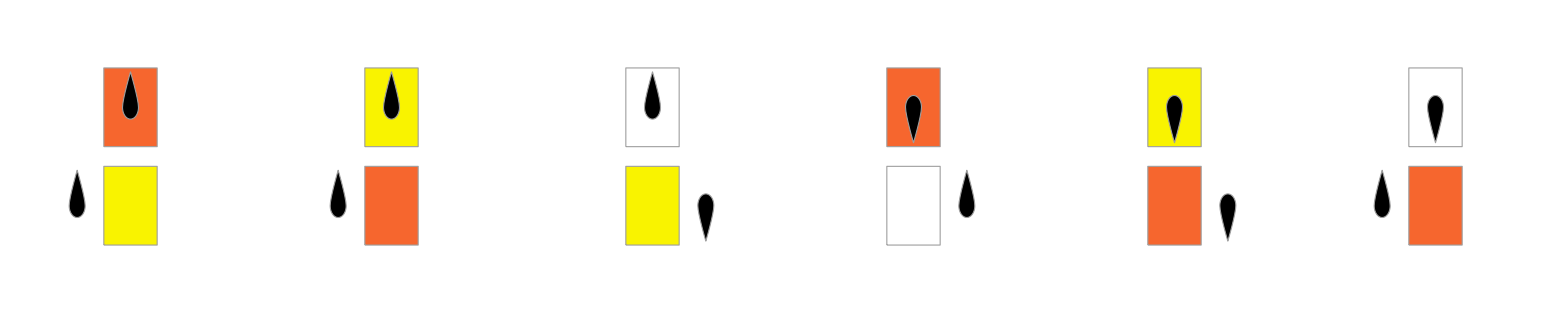

```mathematica
RulePlot[tM]
```

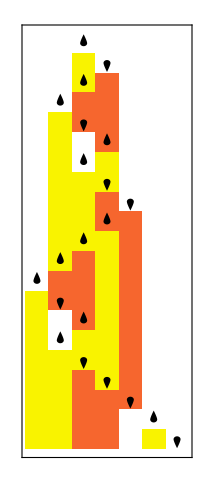

```mathematica
RulePlot[tM,{1,{{},0}},20]
```

```mathematica
tMRule=ResourceFunction["ComputationalSystemRules"][tM];
```

```mathematica
cWTM[TMToCWTM[tMRule],TMToCWTMInit[{1,{0}}],50]//Column
```

{1,{0,R,L}}
{2,{R,L,1}}
{Fl[1,R],{L,1,Ml,2}}
{Fl[1,L],{1,Ml,2,R}}
{Fl[1,1],{Ml,2,R,L}}
{Fl[1,2],{2,R,L,Ml}}
{Fl[1,2],{R,L,Ml,2}}
{Fl[1,R],{L,Ml,2,2}}
{Fl[1,L],{Ml,2,2,R}}
{2,{2,2,R,L,1}}
{1,{2,R,L,1,0}}
{Fl[1,1],{R,L,1,0,Ml}}
{Fl[1,R],{L,1,0,Ml,1}}
{Fl[1,L],{1,0,Ml,1,R}}
{Fl[1,1],{0,Ml,1,R,L}}
{Fl[1,0],{Ml,1,R,L,1}}
{2,{1,R,L,1,1}}
{2,{R,L,1,1,2}}
{Fl[1,R],{L,1,1,2,Ml,2}}
{Fl[1,L],{1,1,2,Ml,2,R}}
{Fl[1,1],{1,2,Ml,2,R,L}}
{Fl[1,1],{2,Ml,2,R,L,1}}
{Fl[1,2],{Ml,2,R,L,1,1}}
{Fl[1,1],{2,R,L,1,1,Ml}}
{Fl[1,2],{R,L,1,1,Ml,1}}
{Fl[1,R],{L,1,1,Ml,1,2}}
{Fl[1,L],{1,1,Ml,1,2,R}}
{Fl[1,1],{1,Ml,1,2,R,L}}
{Fl[1,1],{Ml,1,2,R,L,1}}
{Fl[1,2],{1,2,R,L,1,Ml}}
{Fl[1,1],{2,R,L,1,Ml,2}}
{Fl[1,2],{R,L,1,Ml,2,1}}
{Fl[1,R],{L,1,Ml,2,1,2}}
{Fl[1,L],{1,Ml,2,1,2,R}}
{Fl[1,1],{Ml,2,1,2,R,L}}
{Fl[1,2],{2,1,2,R,L,Ml}}
{Fl[1,2],{1,2,R,L,Ml,2}}
{Fl[1,1],{2,R,L,Ml,2,2}}
{Fl[1,2],{R,L,Ml,2,2,1}}
{Fl[1,R],{L,Ml,2,2,1,2}}
{Fl[1,L],{Ml,2,2,1,2,R}}
{2,{2,2,1,2,R,L,1}}
{1,{2,1,2,R,L,1,0}}
{Fl[1,1],{1,2,R,L,1,0,Ml}}
{Fl[1,1],{2,R,L,1,0,Ml,1}}
{Fl[1,2],{R,L,1,0,Ml,1,1}}
{Fl[1,R],{L,1,0,Ml,1,1,2}}
{Fl[1,L],{1,0,Ml,1,1,2,R}}
{Fl[1,1],{0,Ml,1,1,2,R,L}}
{Fl[1,0],{Ml,1,1,2,R,L,1}}
{2,{1,1,2,R,L,1,1}}

```mathematica
cWTMRule={{1,0}->{2,{0,1}},{2,0}->{2,{2}},{3,0}->{1,{0}},{1,1}->{2,{0}},{2,1}->{3,{1}},{3,1}->{1,{0,0}},{1,2}->{3,{0}},{2,2}->{1,{2,2}},{3,2}->{2,{1}}};
```

```mathematica
cWTM[cWTMRule,{1,{0}},20]//Column
```

{1,{0}}
{2,{0,1}}
{2,{1,2}}
{3,{2,1}}
{2,{1,1}}
{3,{1,1}}
{1,{1,0,0}}
{2,{0,0,0}}
{2,{0,0,2}}
{2,{0,2,2}}
{2,{2,2,2}}
{1,{2,2,2,2}}
{3,{2,2,2,0}}
{2,{2,2,0,1}}
{1,{2,0,1,2,2}}
{3,{0,1,2,2,0}}
{1,{1,2,2,0,0}}
{2,{2,2,0,0,0}}
{1,{2,0,0,0,2,2}}
{3,{0,0,0,2,2,0}}
{1,{0,0,2,2,0,0}}

```mathematica
Grid[cWTM[ColoredToBinCWTM[cWTMRule],ColoredToBinCWTMInit[{1,{0}},cWTMRule],25],Alignment->Left]
```

Li[2,{{0,1}},{0}] | {0}
Li[2,{{1},{0}},{}] | {0,1}
Li[2,{{0}},{0}] | {1,1}
Li[3,{{0},{1}},{}] | {1,0}
Li[3,{{1}},{1}] | {0,0}
Li[2,{{0},{1}},{}] | {0,1}
Li[2,{{1}},{0}] | {1,0}
Li[3,{{0},{1}},{}] | {0,1}
Li[3,{{1}},{0}] | {1,0}
Li[1,{{0,0},{0,0}},{}] | {0,1}
Li[1,{{0,0}},{0}] | {1,0,0}
Li[2,{{0},{0}},{}] | {0,0,0,0}
Li[2,{{0}},{0}] | {0,0,0,0}
Li[2,{{1},{0}},{}] | {0,0,0,0}
Li[2,{{0}},{0}] | {0,0,0,1}
Li[2,{{1},{0}},{}] | {0,0,1,0}
Li[2,{{0}},{0}] | {0,1,0,1}
Li[2,{{1},{0}},{}] | {1,0,1,0}
Li[2,{{0}},{1}] | {0,1,0,1}
Li[1,{{1,0},{1,0}},{}] | {1,0,1,0}
Li[1,{{1,0}},{1}] | {0,1,0,1,0}
Li[3,{{0},{0}},{}] | {1,0,1,0,1,0}
Li[3,{{0}},{1}] | {0,1,0,1,0,0}
Li[2,{{0},{1}},{}] | {1,0,1,0,0,0}
Li[2,{{1}},{1}] | {0,1,0,0,0,0}
Li[1,{{1,0},{1,0}},{}] | {1,0,0,0,0,1}

```mathematica
cWTMBinRule={{0,0}->{1,{0}},{0,1}->{0,{0}},{1,0}->{0,{1,1}},{1,1}->{0,{1}}};
```

```mathematica
cWTM[cWTMBinRule,{1,{0}},20]//Column
```

{1,{0}}
{0,{1,1}}
{0,{1,0}}
{0,{0,0}}
{1,{0,0}}
{0,{0,1,1}}
{1,{1,1,0}}
{0,{1,0,1}}
{0,{0,1,0}}
{1,{1,0,0}}
{0,{0,0,1}}
{1,{0,1,0}}
{0,{1,0,1,1}}
{0,{0,1,1,0}}
{1,{1,1,0,0}}
{0,{1,0,0,1}}
{0,{0,0,1,0}}
{1,{0,1,0,0}}
{0,{1,0,0,1,1}}
{0,{0,0,1,1,0}}
{1,{0,1,1,0,0}}

```mathematica
ResourceFunction["TagSystem"][{2,Replace[(x_->y_):>{x,_}->y]/@CWTMToTag[cWTMBinRule]},CWTMToTagInit[{1,{0}}],50]//Column
```

{H_(2,1),h_(2,1),A_(2,1),A_(2,1),U_(2,1),u_(2,1),U_(2,1),u_(2,1)}
{A_(2,1),A_(2,1),U_(2,1),u_(2,1),U_(2,1),u_(2,1),H_(3,1),$}
{U_(2,1),u_(2,1),U_(2,1),u_(2,1),H_(3,1),$,A_(3,1),A_(3,1)}
{U_(2,1),u_(2,1),H_(3,1),$,A_(3,1),A_(3,1),U_(3,1)}
{H_(3,1),$,A_(3,1),A_(3,1),U_(3,1),U_(3,1)}
{A_(3,1),A_(3,1),U_(3,1),U_(3,1),H_(4,1),h_(4,1)}
{U_(3,1),U_(3,1),H_(4,1),h_(4,1),A_(4,1),a_(4,1)}
{H_(4,1),h_(4,1),A_(4,1),a_(4,1),U_(4,1),u_(4,1),X_(4,1),x_(4,1)}
{A_(4,1),a_(4,1),U_(4,1),u_(4,1),X_(4,1),x_(4,1),H_(1,1),$}
{U_(4,1),u_(4,1),X_(4,1),x_(4,1),H_(1,1),$,A_(1,1),a_(1,1),0}
{X_(4,1),x_(4,1),H_(1,1),$,A_(1,1),a_(1,1),0,U_(1,1),U_(1,1)}
{H_(1,1),$,A_(1,1),a_(1,1),0,U_(1,1),U_(1,1),X_(1,1),X_(1,1)}
{A_(1,1),a_(1,1),0,U_(1,1),U_(1,1),X_(1,1),X_(1,1),H_(2,1),h_(2,1)}
{0,U_(1,1),U_(1,1),X_(1,1),X_(1,1),H_(2,1),h_(2,1),A_(2,1),A_(2,1)}
{U_(1,1),X_(1,1),X_(1,1),H_(2,1),h_(2,1),A_(2,1),A_(2,1)}
{X_(1,1),H_(2,1),h_(2,1),A_(2,1),A_(2,1),U_(2,1),u_(2,1)}
{h_(2,1),A_(2,1),A_(2,1),U_(2,1),u_(2,1),X_(2,1),x_(2,1)}
{A_(2,1),U_(2,1),u_(2,1),X_(2,1),x_(2,1),$,H_(3,1),$}
{u_(2,1),X_(2,1),x_(2,1),$,H_(3,1),$,A_(3,1),A_(3,1)}
{x_(2,1),$,H_(3,1),$,A_(3,1),A_(3,1),V_(3,1)}
{H_(3,1),$,A_(3,1),A_(3,1),V_(3,1),Y_(3,1),Y_(3,1)}
{A_(3,1),A_(3,1),V_(3,1),Y_(3,1),Y_(3,1),H_(4,1),h_(4,1)}
{V_(3,1),Y_(3,1),Y_(3,1),H_(4,1),h_(4,1),A_(4,1),a_(4,1)}
{Y_(3,1),H_(4,1),h_(4,1),A_(4,1),a_(4,1),V_(4,1),v_(4,1),Y_(4,1),y_(4,1)}
{h_(4,1),A_(4,1),a_(4,1),V_(4,1),v_(4,1),Y_(4,1),y_(4,1),Y_(4,1),y_(4,1)}
{a_(4,1),V_(4,1),v_(4,1),Y_(4,1),y_(4,1),Y_(4,1),y_(4,1)}
{v_(4,1),Y_(4,1),y_(4,1),Y_(4,1),y_(4,1),$,P_(5,1),$}
{y_(4,1),Y_(4,1),y_(4,1),$,P_(5,1),$}
{y_(4,1),$,P_(5,1),$,V_(5,1),y_(4,1)}
{P_(5,1),$,V_(5,1),y_(4,1),V_(5,1),y_(4,1)}
{V_(5,1),y_(4,1),V_(5,1),y_(4,1),P_(6,1),$}
{V_(5,1),y_(4,1),P_(6,1),$,V_(6,1),v_(6,1)}
{P_(6,1),$,V_(6,1),v_(6,1),V_(6,1),v_(6,1)}
{V_(6,1),v_(6,1),V_(6,1),v_(6,1),B_(6,1),b_(6,1),B_(6,1),b_(6,1),H_(3,0),$}
{V_(6,1),v_(6,1),B_(6,1),b_(6,1),B_(6,1),b_(6,1),H_(3,0),$,U_(3,0)}
{B_(6,1),b_(6,1),B_(6,1),b_(6,1),H_(3,0),$,U_(3,0),U_(3,0)}
{B_(6,1),b_(6,1),H_(3,0),$,U_(3,0),U_(3,0),B_(3,0),B_(3,0)}
{H_(3,0),$,U_(3,0),U_(3,0),B_(3,0),B_(3,0),B_(3,0),B_(3,0)}
{U_(3,0),U_(3,0),B_(3,0),B_(3,0),B_(3,0),B_(3,0),H_(4,0),h_(4,0)}
{B_(3,0),B_(3,0),B_(3,0),B_(3,0),H_(4,0),h_(4,0),U_(4,0),u_(4,0),X_(4,0),x_(4,0)}
{B_(3,0),B_(3,0),H_(4,0),h_(4,0),U_(4,0),u_(4,0),X_(4,0),x_(4,0),B_(4,0),b_(4,0)}
{H_(4,0),h_(4,0),U_(4,0),u_(4,0),X_(4,0),x_(4,0),B_(4,0),b_(4,0),B_(4,0),b_(4,0)}
{U_(4,0),u_(4,0),X_(4,0),x_(4,0),B_(4,0),b_(4,0),B_(4,0),b_(4,0),H_(1,0),$}
{X_(4,0),x_(4,0),B_(4,0),b_(4,0),B_(4,0),b_(4,0),H_(1,0),$,U_(1,0),U_(1,0)}
{B_(4,0),b_(4,0),B_(4,0),b_(4,0),H_(1,0),$,U_(1,0),U_(1,0),X_(1,0),X_(1,0)}
{B_(4,0),b_(4,0),H_(1,0),$,U_(1,0),U_(1,0),X_(1,0),X_(1,0),B_(1,0),b_(1,0),0}
{H_(1,0),$,U_(1,0),U_(1,0),X_(1,0),X_(1,0),B_(1,0),b_(1,0),0,B_(1,0),b_(1,0),0}
{U_(1,0),U_(1,0),X_(1,0),X_(1,0),B_(1,0),b_(1,0),0,B_(1,0),b_(1,0),0,H_(2,0),h_(2,0)}
{X_(1,0),X_(1,0),B_(1,0),b_(1,0),0,B_(1,0),b_(1,0),0,H_(2,0),h_(2,0),U_(2,0),u_(2,0)}
{B_(1,0),b_(1,0),0,B_(1,0),b_(1,0),0,H_(2,0),h_(2,0),U_(2,0),u_(2,0),X_(2,0),x_(2,0)}
{0,B_(1,0),b_(1,0),0,H_(2,0),h_(2,0),U_(2,0),u_(2,0),X_(2,0),x_(2,0),B_(2,0),B_(2,0)}

```mathematica
tagRule={2->{0,2,1,2},1->{0},0->{2,1}};
```

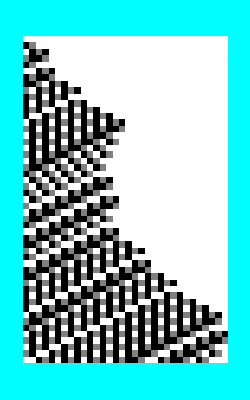

```mathematica
ArrayPlot[ResourceFunction["TagSystem"][{2,Replace[(x_->y_):>{x,_}->y]/@tagRule},{0,0},50],Background->Cyan]
```

```mathematica
Tag1ToCT[tagRule]
```

Tag1ToCT[{2→{0,2,1,2},1→{0},0→{2,1}}]

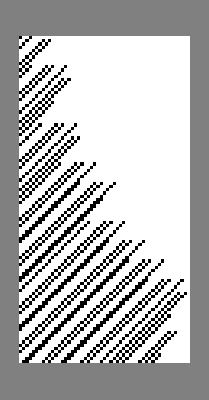

```mathematica
ArrayPlot[ResourceFunction["CyclicTagSystem"][Tag1ToCT[{2,tagRule}],Tag1ToCTInit[{0,0},tagRule],100],Background->Gray]
```